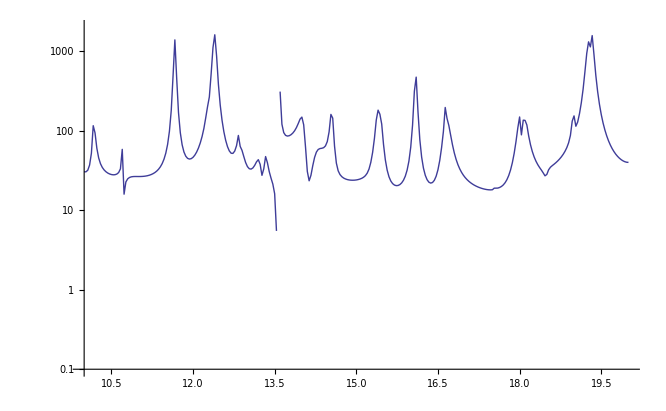

```mathematica
(* read in the raw ENDF data for Uranium 235 and plot the cross section according to the Reich-Moore formalism *)

Clear["Global`*"];
SetDirectory["C:\\temp\\matlab\\n-ENDF-VII0.endf\\"];

EndfStream=OpenRead["n-092_U_235.endf"];
MAT=9228;
MF=2;
MT=151;
searchword=ToString[PaddedForm[MAT,4-1]]<>ToString[PaddedForm[MF,2-1]]<>ToString[MT];
myline=Read[EndfStream,String];
While[myline≠"EndOfFile",myline=Read[EndfStream,String];myline=" "<>StringTake[myline,{67,80}];If[Length[StringPosition[myline,searchword,1]]>0,Break[];]];

myline=Read[EndfStream,String];
myline=Read[EndfStream,String];
EL=ToExpression[StringReplace[StringTake[myline,{1,11}],{"-"->" 10^-","+"->" 10^+"}]];
EH=ToExpression[StringReplace[StringTake[myline,{12,22}],{"-"->" 10^-","+"->" 10^+"}]];
myline=Read[EndfStream,String];
SPI=ToExpression[StringReplace[StringTake[myline,{1,11}],{"-"->" 10^-","+"->" 10^+"}]];
AP=ToExpression[StringReplace[StringTake[myline,{12,22}],{"-"->" 10^-","+"->" 10^+"}]];
myline=Read[EndfStream,String];
AWRI=ToExpression[StringReplace[StringTake[myline,{1,11}],{"-"->" 10^-","+"->" 10^+"}]];
APL=ToExpression[StringReplace[StringTake[myline,{12,22}],{"-"->" 10^-","+"->" 10^+"}]];
L=ToExpression[StringReplace[StringTake[myline,{23,33}],{"-"->" 10^-","+"->" 10^+"}]];
NRI=ToExpression[StringReplace[StringTake[myline,{56,66}],{"-"->" 10^-","+"->" 10^+"}]];

RMoore=Table[{0,0,0,0,0,0},{j,NRI}];

For[j=1,j≤NRI,j++,myline=Read[EndfStream,String];RMoore[[j]][[1]]=ToExpression[StringTake[myline,{1,1}]<>StringReplace[StringTake[myline,{1+1,11}],{"-"->" 10^-","+"->" 10^+"}]];RMoore[[j]][[2]]=ToExpression[StringTake[myline,{12,12}]<>StringReplace[StringTake[myline,{12+1,22}],{"-"->" 10^-","+"->" 10^+"}]];
RMoore[[j]][[3]]=ToExpression[StringTake[myline,{23,23}]<>StringReplace[StringTake[myline,{23+1,33}],{"-"->" 10^-","+"->" 10^+"}]];
RMoore[[j]][[4]]=ToExpression[StringTake[myline,{34,34}]<>StringReplace[StringTake[myline,{34+1,44}],{"-"->" 10^-","+"->" 10^+"}]];
RMoore[[j]][[5]]=ToExpression[StringTake[myline,{45,45}]<>StringReplace[StringTake[myline,{45+1,55}],{"-"->" 10^-","+"->" 10^+"}]];
RMoore[[j]][[6]]=ToExpression[StringTake[myline,{56,56}]<>StringReplace[StringTake[myline,{56+1,66}],{"-"->" 10^-","+"->" 10^+"}]];];

mn=939.565560 10^6;
hbar=6.582119 10^-16;
cspeed=299792458;

kn[x_]:=Sqrt[2*mn*Abs[x]/(cspeed*cspeed*hbar*hbar)]*AWRI/(AWRI+1);
P0[x_]:=AP*kn[x]*10^-14;
gJ[x_,y_]:=(2*x+1)/(2*(2*y+1));
phi0[x_]:=AP*kn[x]*10^-14;

RMatrixM11[x_,NRJ_]:=Sign[RMoore[[NRJ]][[3]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[3]]]/P0[RMoore[[NRJ]][[1]]]]*Sign[RMoore[[NRJ]][[3]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[3]]]/P0[RMoore[[NRJ]][[1]]]]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);
RMatrixM12[x_,NRJ_]:=Sign[RMoore[[NRJ]][[3]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[3]]]/P0[RMoore[[NRJ]][[1]]]]*Sign[RMoore[[NRJ]][[5]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[5]]]/1]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);
RMatrixM13[x_,NRJ_]:=Sign[RMoore[[NRJ]][[3]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[3]]]/P0[RMoore[[NRJ]][[1]]]]*Sign[RMoore[[NRJ]][[6]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[6]]]/1]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);

RMatrixM21[x_,NRJ_]:=RMatrixM12[x,NRJ];
RMatrixM22[x_,NRJ_]:=Sign[RMoore[[NRJ]][[5]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[5]]]/1]*Sign[RMoore[[NRJ]][[5]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[5]]]/1]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);
RMatrixM23[x_,NRJ_]:=Sign[RMoore[[NRJ]][[5]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[5]]]/1]*Sign[RMoore[[NRJ]][[6]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[6]]]/1]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);

RMatrixM31[x_,NRJ_]:=RMatrixM13[x,NRJ];
RMatrixM32[x_,NRJ_]:=RMatrixM23[x,NRJ];
RMatrixM33[x_,NRJ_]:=Sign[RMoore[[NRJ]][[6]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[6]]]/1]*Sign[RMoore[[NRJ]][[6]]]*Sqrt[0.5*Abs[RMoore[[NRJ]][[6]]]/1]/(RMoore[[NRJ]][[1]]-x-0.5*ⅈ*RMoore[[NRJ]][[4]]/1);

RMatrix[x_,NRJ_]:={{RMatrixM11[x,NRJ],RMatrixM12[x,NRJ],RMatrixM13[x,NRJ]},{RMatrixM21[x,NRJ],RMatrixM22[x,NRJ],RMatrixM33[x,NRJ]},{RMatrixM31[x,NRJ],RMatrixM32[x,NRJ],RMatrixM33[x,NRJ]}};

TablJ3={};
TablJ4={};
For[j=1,j≤NRI,j++,If[RMoore[[j]][[2]]==3.0,AppendTo[TablJ3,j],AppendTo[TablJ4,j]]];

RSMatrixJ3[x_]:=Sum[RMatrix[x,j],{j,TablJ3}];
RSMatrixJ4[x_]:=Sum[RMatrix[x,j],{j,TablJ4}];

PMatrix[x_]:={{Sqrt[P0[x]],0,0},{0,Sqrt[1],0},{0,0,Sqrt[1]}};
LMatrix[x_]:={{1/(ⅈ*P0[x]),0,0},{0,1/ⅈ,0},{0,0,1/ⅈ}};

XMatrixJ3[x_]:=PMatrix[x].LMatrix[x].Inverse[LMatrix[x]-RSMatrixJ3[x]].RSMatrixJ3[x].PMatrix[x];
XMatrixJ4[x_]:=PMatrix[x].LMatrix[x].Inverse[LMatrix[x]-RSMatrixJ4[x]].RSMatrixJ4[x].PMatrix[x];

Xi11J3[x_]:=Im[XMatrixJ3[x][[1]][[1]]];
Xr11J3[x_]:=Re[XMatrixJ3[x][[1]][[1]]];

Xi11J4[x_]:=Im[XMatrixJ4[x][[1]][[1]]];
Xr11J4[x_]:=Re[XMatrixJ4[x][[1]][[1]]];


sigmaTJ3[x_]:=(4*π)/(kn[x]*kn[x])*gJ[3,3.5]*(Sin[phi0[x]]*Sin[phi0[x]]+Xi11J3[x]*Cos[2*phi0[x]]-Xr11J3[x]*Sin[2*phi0[x]])/10^-28;
sigmaTJ4[x_]:=(4*π)/(kn[x]*kn[x])*gJ[4,3.5]*(Sin[phi0[x]]*Sin[phi0[x]]+Xi11J4[x]*Cos[2*phi0[x]]-Xr11J4[x]*Sin[2*phi0[x]])/10^-28;
sigmaT[x_]:=sigmaTJ3[x]+sigmaTJ4[x];

TablXS={};
NK=300;
e1=10;
e2=20;
For[j=0,j≤NK,j++,AppendTo[TablXS,{e1+j*(e2-e1)/NK,sigmaT[e1+j*(e2-e1)/NK]}]];
ListLogPlot[TablXS,Joined->True,PlotRange->{{e1,e2},{0.1,2000}}]
```

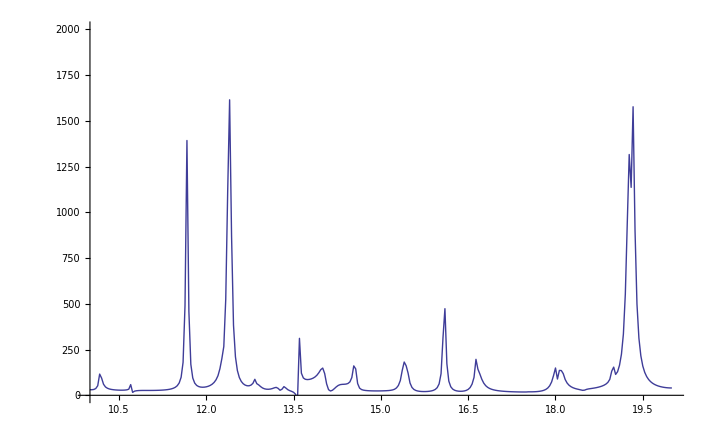

```mathematica
ListPlot[TablXS,Joined->True,PlotRange->{{e1,e2},{0.1,2000}}]
```

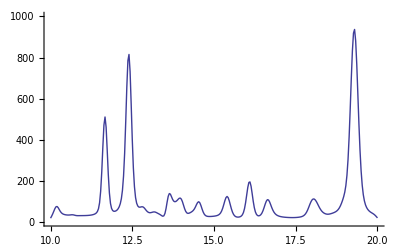

```mathematica
temp=500;
m=1;
M=235;
kB=8.617343 10^-5;
deltaD=Sqrt[m*kB*temp/M];
ff[x_]:=Interpolation[TablXS,x];
sigmaT0[x_]:=Piecewise[{{ff[x],10<x<20},{0,x≤10},{0,x≥20}}];
(* Plot[sigmaT0[x],{x,10,20},PlotRange->{{e1,e2},{0.1,2000}}] *)


sigmatilde[w_]:=Piecewise[{{ff[w^2],w>0},{0,w==0},{-ff[w^2],w<0}}];
sigmaTD[x_,w_]:=(1/(deltaD*Sqrt[π]*x))*w^2*Exp[-(Sqrt[x]-w)^2/deltaD^2]*sigmatilde[w];
sigmaTDI[x_]:=NIntegrate[sigmaTD[x,w],{w,Sqrt[10],Sqrt[20]}];

TablXSD={};
For[j=0,j≤NK,j++,AppendTo[TablXSD,{e1+j*(e2-e1)/NK,sigmaTDI[e1+j*(e2-e1)/NK]}]];
ListPlot[TablXSD,Joined->True,PlotRange->{{e1,e2},{0,1000}}]
```